# Amateur Sleuthing of NK Nuclear Tests

```mathematica
EarthquakeData[Entity["Country","NorthKorea"],4,{Now-Quantity[15, "Years"], Now-Quantity[1, "Years"]}];
```

```mathematica
times=Values[%46[[All,"Period"]]]
```

{Mon 9 Oct 2006 01:35:28GMT+1.,Mon 25 May 2009 00:54:43GMT+1.,Tue 12 Feb 2013 02:57:51GMT+1.,Wed 6 Jan 2016 01:30:01GMT+1.,Fri 9 Sep 2016 00:30:02GMT+1.,Sun 3 Sep 2017 03:30:02GMT+1.,Sun 3 Sep 2017 03:38:32GMT+1.}

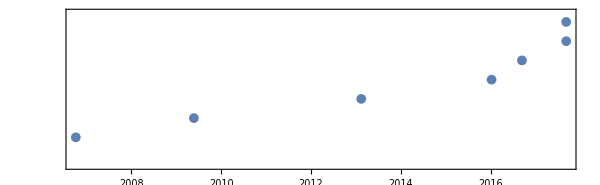

```mathematica
TimelinePlot[times,PlotLayout->"Stacked"]
```

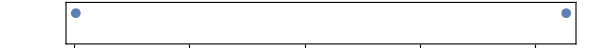

```mathematica
TimelinePlot[Take[times,{-2,-1}]]
```

```mathematica
locations = Values[%[[All,"Position"]]]
```

{GeoPosition[{41.294,129.093}],GeoPosition[{41.3058,129.029}],GeoPosition[{41.3075,129.076}],GeoPosition[{41.308,129.049}],GeoPosition[{41.2977,129.015}],GeoPosition[{41.3429,129.036}],GeoPosition[{41.35,129.03}]}

```mathematica
Table[GeoListPlot[MapIndexed[Labeled[#,First[#2]]&,locations],GeoBackground->"ReliefMap",GeoRange->ranges],{ranges,{Quantity[5, "Miles"],Quantity[20, "Miles"]}}]
```

{-Graphics-,-Graphics-}

```mathematica
GeoImage[Take[locations,-2],GeoRange->Quantity[500, "Feet"]]
```

-Graphics-

```mathematica
ListPlot3D[GeoElevationData[locations], MeshFunctions->{#3 &}]
```

-Graphics3D-

```mathematica
GeoNearest["City",locations[[02]],5]
```

{Svngjibaegam,Hau,Myongchon,Myongan,Kilchu}

```mathematica
GeoListPlot[Flatten[{Labeled[GeoDisk[Entity["City",{"Svngjibaegam","Yanggang","NorthKorea"}],Quantity[5, "Miles"]],Entity["City",{"Svngjibaegam","Yanggang","NorthKorea"}]],locations}]]
```

```mathematica
EntityList[];
```

```mathematica
Length[%]
```

2431

```mathematica
GeoListPlot[%75]
```

-Graphics-

```mathematica
RandomEntity["NuclearExplosion",5]
```

{Dynamika, hole A-100,China #17,K Project K2,Toggle Akbar,USSR #543}

```mathematica
Labeled[GeoImage[#,GeoRange->LinguisticAssistant],#]&/@%103
```

{-Graphics-Dynamika, hole A-100,-Graphics-China #17,-Graphics-K Project K2,-Graphics-Toggle Akbar,-Graphics-USSR #543}

```mathematica
Entity["NuclearExplosion","UnitedStates11091972Test1"]["Dataset"]
```

Dataset[<>]

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[Entity["NuclearExplosion","UnitedStates11091972Test1"],Quantity[1, "Miles"]]],MeshFunctions->{#3&}]
```

-Graphics3D-